# Quantum Teleportation in Wolfram Model

Muhammad Taufiq Murtadho

Korea Advanced Institute of Science and Technology

Abstract: Entanglement is a valuable resource for many quantum communication tasks. One example of such tasks is quantum teleportation where a quantum state is transferred between two spatially separated parties by performing only local operations and classical communication (LOCC). In this project, we explore the analog of quantum teleportation in the Wolfram model by looking at string substitution systems. In other words, we investigate whether we can teleport a string from one spatial location to the other by using entanglement in branchial space. 

Objective: Generate events on a string multiway system that can be interpreted as a quantum teleportation phenomenon.

Computational Plan/Strategy: First, we identify a string transformation pattern that correspond to quantum teleportation. Then, we develop a program to scan through a multiway system to spot the pattern. Then, we apply the program to a class of string substitution rules that can potentially display quantum teleportation phenomenon.

## Wolfram Community Post (material for blog post)

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

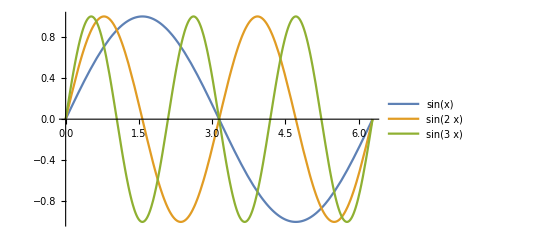

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

## Complete project work

Consider the typical communication setup: Bob (denoted by B) wants to send a message (C) to Alice (denoted by A). The classical way of doing this would be

Bob copies the message

Bob sends the message through a channel (X)

Alice receives the message

The whole protocol can be simulated in string substitution system as follows.

String substitution system for classical communication protocol
Idea: Make this as a model of how to teleport classical information

```mathematica
ResourceFunction["MultiwaySystem"][{"BC"-> "CB","XC"-> "CX","AC"-> "CA"},"AXXXBC",6,"StatesGraph"]
```

-Graphics-

As expected, the information transfer requires as many step as the distance between Alice and Bob. This is because we insist on locality (no information travels faster than light) when we transfer the information through the channel X (represented by string substitution rule “XC”→”CX”). This means that if Alice and Bob are further apart, they need to apply this rule many more times. Consequently, the path length required for this protocol would become longer the further Alice and Bob are.

#### Entanglement and Non-local correlation

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "C"},"AXXXXBC",3,"EvolutionCausalGraph"]
```

-Graphics-

This system would teleport C to Alice in exactly three steps no matter how far the distance between Alice and Bob is. Moreover, it is important to notice that “C” can only be sent to A by virtue of its connection to B (in other words, we have no rule such as A→C). Secondly, we also do not use channel communication (we have no rule involving X). Lastly, the system is causal invariant so it is consistent with the fact that quantum teleportation protocol requires a measurement to be made.

#### Discussion: No-cloning theorem

This demonstrate non-local correlation of entanglement.

```mathematica
HighlightGraph[ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "C"},"AXXBC",3,"StatesGraphStructure"], {Style["AXXBC",Red],Style["BXXBC",Red],Style["BXXCC",Red],Style[ "CXXCC",Red]},VertexLabels->Automatic]
```

-Graphics-

If C is presumed to be an unknown quantum state, the model above seem to violate no-cloning theorem. Alternatively, we can avoid violating no-cloning theorem if we assume C is known by B. The interpretation then becomes quite clear at least when we follow the history marked by red. First, the state of A and B becomes maximally correlated. Then, B is measured with respect to C basis. As a result, the state of A also collapses to C. Thus, this model is not yet “full” quantum teleportation in which C can be teleported even if B does not know the state C. Rather, this is a form of “teleportation” when we do not include Bell measurement and classical information transfer.

#### Quantum Teleportation

Now, we denote 0 → A and 1→ B, so that two particle system is spanned by string bases: AA, AB, BA, BB. Initially, Alice and Bob shares a Bell state of the form (AA+BB) and Bob has an unknown qubit state C=αA+βB. Between Alice and Bob, we have (quantum) communication channel X. We model teleportation and direct communication by the following string system.

```mathematica
ResourceFunction["MultiwaySystem"][{"C"-> "A","C"-> "B"},{"AXAC","BXBC"},1,"EvolutionGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

Bell measurement completion rules

```mathematica
BellCompletion={"BA"-> "AA", "AA"-> "BA","BA"-> "BB","BB"-> "BA", "AB"-> "AA","AA"-> "AB", "AB"-> "BB","BB"-> "AB"};
ResourceFunction["MultiwaySystem"][BellCompletion,{"AA","BB","AB","BA"},1,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"C"-> "A","C"-> "A","C"-> "A","C"-> "B"},BellCompletion],{"AXAC","BXBC"},2,"EvolutionGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

AA±BB bell basis: 3B+2A → Can be corrected by an X-gate
AB±BA bell basis: 2B + 3A → Correct state

How to produce initial entangled state without ruining the evolution?

```mathematica
ResourceFunction["MultiwaySystem"][{"D"-> "AXA","D"-> "BXB","C"-> "A","C"-> "B"},"DC",2,"EvolutionCausalGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"D"-> "AXA","D"-> "BXB","C"-> "A","C"-> "A","C"-> "A","C"-> "B"},BellCompletion],"DC",3,"EvolutionGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

This seems to work!

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"D"-> "AXA","D"-> "BXB","C"-> "A","C"-> "A","C"-> "A","C"-> "B"},BellCompletion],"DC",3,"CausalInvariantQ"]
```

False

The system is not causal invariant! Which reflects the fact that Alice state after teleportation is still coherent.

## Keywords

Quantum Information

Quantum Teleportation

Entanglement

String substitution system

## Acknowledgment

Mentor: Marco Thiel

<text>

## References

<Ref1>

<Ref2>

...